```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./LPAp_mub0/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub0/buffer/Zphi.dat"]];
T0=Flatten[Import["./LPAp_mub0/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]/√Zphi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub0linear=Transpose[{T0[[2;;Length[t]-2]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["./LPAp_mub300/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub300/buffer/Zphi.dat"]];
T300=Flatten[Import["./LPAp_mub300/buffer/TMeV.dat"]];
t=-(T300-T300[[1]])/T300[[1]];
datamub300=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]*√Zphi[[2;;Length[t]]]]}];
b1mub300=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];
b1mub300linear=Transpose[{T300[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];

fpi=Flatten[Import["./LPAp_mub400/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub400/buffer/Zphi.dat"]];
T400=Flatten[Import["./LPAp_mub400/buffer/TMeV.dat"]];
t=-(T400-T400[[1]])/T400[[1]];
datamub400=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]*√Zphi[[2;;Length[t]]]]}];
b1mub400=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];
b1mub400linear=Transpose[{T400[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];

fpi=Flatten[Import["./LPAp_mub500/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub500/buffer/Zphi.dat"]];
T500=Flatten[Import["./LPAp_mub500/buffer/TMeV.dat"]];
t=-(T500-T500[[1]])/T500[[1]];
datamub500=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]*√Zphi[[2;;Length[t]]]]}];
b1mub500=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];
b1mub500linear=Transpose[{T500[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];

fpi=Flatten[Import["./LPAp_mub530/buffer/mSigma.dat"]];
Zphi=Flatten[Import["./LPAp_mub530/buffer/Zphi.dat"]];
T530=Flatten[Import["./LPAp_mub530/buffer/TMeV.dat"]];
t=-(T530-T530[[1]])/T530[[1]];
datamub530=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]*√Zphi[[2;;Length[t]]]]}];
b1mub530=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub530[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T530]-2}]]}];
b1mub530linear=Transpose[{T530[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub530[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T530]-2}]]}];
```

## Plot

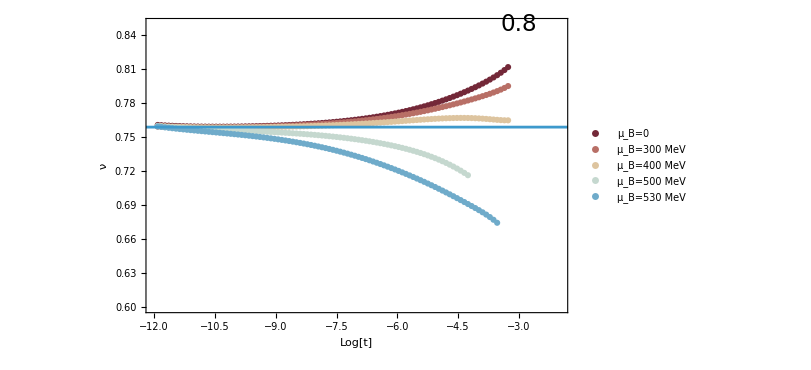

```mathematica
plotT=Show[ListPlot[{Re[b1mub0],Re[b1mub300],Re[b1mub400],Re[b1mub500],Re[b1mub530]},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.2}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0","μ_B=300 MeV","μ_B=400 MeV","μ_B=500 MeV","μ_B=530 MeV"},LabelStyle->16],{0.23,0.32}],
PlotRange->{{-12,-2},{0.6,0.85}},AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.759},{10,0.759}}],ImageSize->600,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.85}]}]
```

```mathematica
Export["./LOdata/mub0data.dat",b1mub0];
Export["./LOdata/mub300data.dat",b1mub300];
Export["./LOdata/mub400data.dat",b1mub400];
Export["./LOdata/mub500data.dat",b1mub500];
Export["./LOdata/mub530data.dat",b1mub530];
```